# Cohen SutherLand

```mathematica
Find4BitCode[min_List, max_List, point_List] := Module[{x, y, code = {0, 0, 0, 0}},
  {x, y} = point;
  If[y > max[[2]], code[[1]] = 1]; 
  If[y < min[[2]], code[[2]] = 1]; 
  If[x > max[[1]], code[[3]] = 1]; 
  If[x < min[[1]], code[[4]] = 1]; 
  code
];
```

```mathematica
Find4BitCode[{-150, -150}, {150,150}, {200,0}]
```

{0,0,1,0}

```mathematica
cohenSutherlandClip[{x1_, y1_}, {x2_, y2_}, {xmin_, xmax_, ymin_, ymax_}] := 
 Module[{outcode1, outcode2, accept = False, x, y, p1, p2},
  
  p1 = {x1, y1};
  p2 = {x2, y2};
  outcode1 = computeOutCode[p1, {xmin, xmax, ymin, ymax}];
  outcode2 = computeOutCode[p2, {xmin, xmax, ymin, ymax}];
  
  While[True,
   If[BitOr[outcode1, outcode2] == 0,
    accept = True;
    Break[],
    If[BitAnd[outcode1, outcode2] != 0,
     Break[],
     
     With[{outcodeOut = If[outcode1 != 0, outcode1, outcode2]},
      If[BitAnd[outcodeOut, TOP] != 0,
       x = p1[[1]] + (p2[[1]] - p1[[1]])*(ymax - p1[[2]])/(p2[[2]] - p1[[2]]);
       y = ymax,
      If[BitAnd[outcodeOut, BOTTOM] != 0,
       x = p1[[1]] + (p2[[1]] - p1[[1]])*(ymin - p1[[2]])/(p2[[2]] - p1[[2]]);
       y = ymin,
      If[BitAnd[outcodeOut, RIGHT] != 0,
       y = p1[[2]] + (p2[[2]] - p1[[2]])*(xmax - p1[[1]])/(p2[[1]] - p1[[1]]);
       x = xmax,
      If[BitAnd[outcodeOut, LEFT] != 0,
       y = p1[[2]] + (p2[[2]] - p1[[2]])*(xmin - p1[[1]])/(p2[[1]] - p1[[1]]);
       x = xmin;
       ]]]];
      
      If[outcodeOut == outcode1,
       p1 = {x, y};
       outcode1 = computeOutCode[p1, {xmin, xmax, ymin, ymax}],
       p2 = {x, y};
       outcode2 = computeOutCode[p2, {xmin, xmax, ymin, ymax}]
       ];
      ]
     ]
    ]
   ];
  
  If[accept, {p1, p2}, None]
];
```

{{-100,0},{-150,-100}}

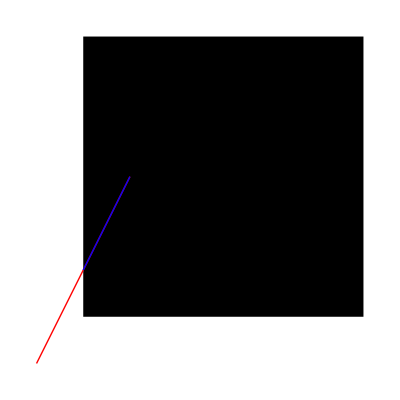

```mathematica
{xmin, ymin} = {-150, -150};
{xmax, ymax} = {150,150};
lineStart = {-100,0};
lineEnd = {-200,-200};

clippedLine = cohenSutherlandClip[lineStart, lineEnd, {xmin, xmax, ymin, ymax}];
Print[clippedLine];
If[clippedLine =!= None,
 Graphics[{
   Rectangle[{xmin, ymin}, {xmax, ymax}],
   Red, Line[{lineStart, lineEnd}],
   Blue, Thick, Line[clippedLine]
   }],
 Print["Line is outside the clipping window."]
]
```